```mathematica
speed[p_]:=Log10[p] p^1.1+p-1
```

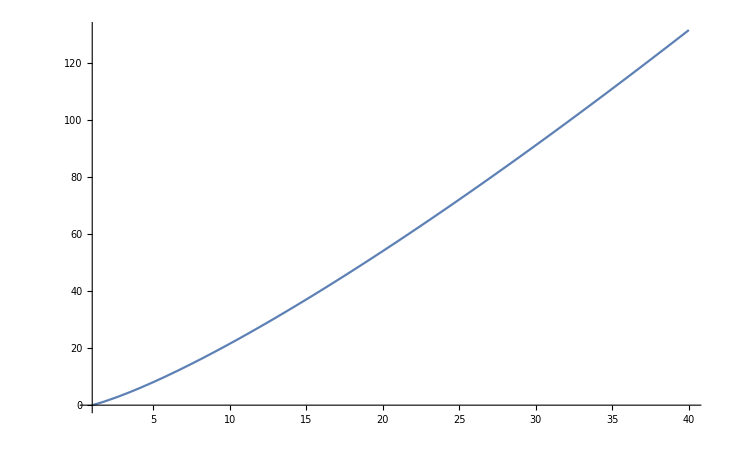

```mathematica
Plot[speed[p],{p,1,40}]
```

```mathematica
Series[speed[p],{p,15,1}]
```

37.1282+3.26543 (p-15)+O[p-15]^2

```mathematica
Normal[37.12817725833908+3.2654348333723484 (p-15)+O[p-15]^2]
```

37.1282+3.26543 (-15+p)

```mathematica
speed[96]
```

395.373

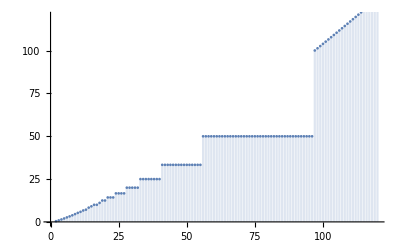

```mathematica
DiscretePlot[Piecewise[{{1,p==1},{100/Ceiling[400/speed[p]],speed[p]≤400},{100 speed[p]/400,True}}],{p,1,120},ImageSize->Full,PlotRange->{0,120}]
```

```mathematica
Maximize[{1/Ceiling[400/speed[p]]/Log[p],p>21},p,Integers]
```

{0.052443,{p→24}}